```mathematica
AlphaTest[x_]:=0≤x≤25
TextCode[text_]:=Select[
					ToCharacterCode[
						ToUpperCase[text]]-65,AlphaTest];
FromCode[textcode_]:=FromCharacterCode[textcode+65];
```

```mathematica
message=Import["http://www.repubblica.it"];
Italian=Import["http://www.corriere.it"];
English=Import["http://www.nytimes.com"];
```

```mathematica
message="GVCDPMUUZE KVEMBNVCDZ CUIJPFLRJA MNCDEGNDMR CZTIMYZEZE
            051 YUOVQGYTHV QZXJACZXVA MVCIVLHBZA RLTNREBXOR AVCQVCURMR
            101 BLGZCCYDXU CUDIPGZXHR RATNFCJDIG SAIVDSLAGN ZBDINTVVGV
            151 YJWZFYWTQN GTEDREHGZA CSAJEBPGXN ZHAZRLLANH QJXONPUTHV
            201 APPGFSVVMN LUTHVAVTIE GJDDIEPPXP FLEZEOBTNG YWPMGCSPNG
            251 MYXVNRATNG YJDHRPPJNP GZHZNBHGHN PLRJARYDLH CSGZVJKJXN
            261 BPHVIMPPVP SPUZPCWTMQ CYEDHBBCVP GAIVPMTTMV SZRDFQLPAN
";
```

```mathematica
XN=TextCode[message];
XN2=TextCode[Italian];
XN3=TextCode[English];

pita=Table[N@Count[XN2,i]/Length[XN2],{i,0,25}]
peng=Table[N@Count[XN3,i]/Length[XN3],{i,0,25}]
```

{0.114883,0.0106243,0.0445696,0.0408628,0.103441,0.0120545,0.0215405,0.00820175,0.127842,0.00037944,0.00151776,0.06827,0.0278451,0.0680657,0.0903651,0.0256268,0.00151776,0.0674528,0.0474008,0.0611774,0.0250139,0.0176294,0.00116751,0.000321065,0.00215989,0.0100698}

{0.0853692,0.0165527,0.0372437,0.0331055,0.0959446,0.0186065,0.0214573,0.0283542,0.0717592,0.00165527,0.00864421,0.0460718,0.0227447,0.0834074,0.0752843,0.0294271,0.00147135,0.0659351,0.0688471,0.104129,0.0202618,0.0179628,0.0177789,0.00260552,0.0241854,0.00119548}

```mathematica
?Count
```

```mathematica
Count[XN2,1]
```

394

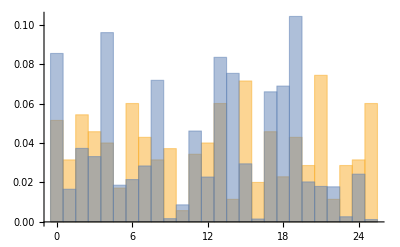

```mathematica
Histogram[{XN,XN3},26,"Probability"]
```

```mathematica
CoincidenceIndex[text_]:=
(
code=TextCode[text];


)
```

```mathematica
XN
```

{0,1,1,14,13,0,19,8,12,4,13,20,2,4,17,2,0,0,1,1,15678,3,8,19,14,17,8,0,11,4,18,15,0,15,8,21,0,8,18,18,13}
 |  |  |  |

```mathematica
Range[0,25]
```

```mathematica
f[x_]:=x+65
```

```mathematica
(#+65)&[4]
```

69

```mathematica
f[4]
```

69

```mathematica
{#,FromCharacterCode[#+65]}& 

g[x_]:={x,FromCharacterCode[x+65]}
Map[g,Range[0,25]]

TableForm@Map[{#,FromCharacterCode[#+65]}&,Range[0,25]]
```

```mathematica
MatrixForm[{{a,b},{c,d}}]
```

(a | b
c | d)

```mathematica
Tally[XN]
f(f-1)


XN
```

{{0,1735},{1,197},{14,1448},{13,1185},{19,867},{8,2269},{12,393},{4,1397},{20,353},{2,753},{17,990},{16,20},{3,813},{21,395},{6,299},{25,179},{15,393},{11,999},{18,680},{7,109},{5,177},{22,18},{24,15},{23,5},{10,21},{9,8}}

(-1+f) f

{0,1,1,14,13,0,19,8,12,4,13,20,2,4,17,2,0,0,1,1,15678,3,8,19,14,17,8,0,11,4,18,15,0,15,8,21,0,8,18,18,13}
 |  |  |  |

```mathematica
1735 1734
```

3008490

```mathematica
FullForm[{a,b,c}]
```

```mathematica
List[a,b,c]
Plus[a,b,c]
```

```mathematica
For@@{a,b,c}
```

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
CoincidenceIndex[textcode_]:=N[Plus@@Map[#[[2]](#[[2]]-1)&,Tally[textcode]]/(Length[textcode](Length[textcode]-1))]
```

```mathematica
CoincidenceIndex[XN]
monoblocks=Transpose@Partition[XN,5];
monoblocks[[2]]
```

```mathematica
CoincidenceIndex[monoblocks[[2]]]
```

0.068323

```mathematica
MutualCoincidenceIndex[TextDecryption[ShiftDecode,19,monoblocks[[2]]],pita]
```

0.0719906

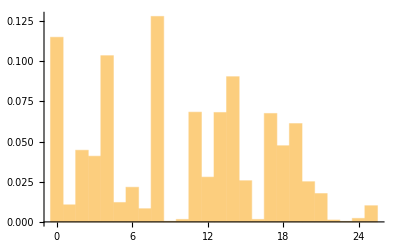

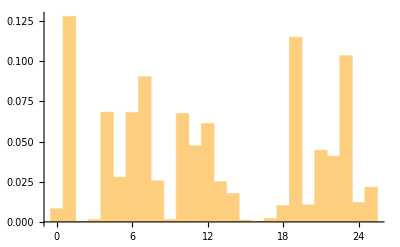

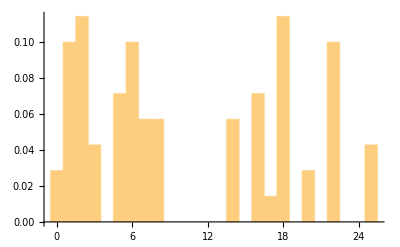

```mathematica
Histogram[XN2,26,Probability]
Histogram[TextEncryption[ShiftEncode,19,XN2],26,Probability]
Histogram[Mod[monoblocks[[2]]-19,26],26,Probability]
```

```mathematica
Reverse@Map[{FromCode[#[[1]]],#}&,SortBy[Tally[monoblocks[[2]]],Last]]
```

{{V,{21,8}},{L,{11,8}},{Z,{25,7}},{U,{20,7}},{P,{15,7}},{Y,{24,5}},{J,{9,5}},{H,{7,4}},{B,{1,4}},{A,{0,4}},{W,{22,3}},{S,{18,3}},{T,{19,2}},{N,{13,2}},{K,{10,1}}}

```mathematica
Table[{a={i,ShiftEncode[19,i]},FromCode[a]},{i,0,25}]
```

{{{0,19},AT},{{1,20},BU},{{2,21},CV},{{3,22},DW},{{4,23},EX},{{5,24},FY},{{6,25},GZ},{{7,0},HA},{{8,1},IB},{{9,2},JC},{{10,3},KD},{{11,4},LE},{{12,5},MF},{{13,6},NG},{{14,7},OH},{{15,8},PI},{{16,9},QJ},{{17,10},RK},{{18,11},SL},{{19,12},TM},{{20,13},UN},{{21,14},VO},{{22,15},WP},{{23,16},XQ},{{24,17},YR},{{25,18},ZS}}

```mathematica
Manipulate[Histogram[{monoblocks[[2]],TextEncryption[ShiftEncode,19,XN2]},26,Probability],{k,0,26,1}]
```

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[XN2,0].

Mod::argt: Mod called with 0 arguments; 2 or 3 arguments are expected.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{3,4,18,10,19,14,15,18,4,25,«35079»},0].

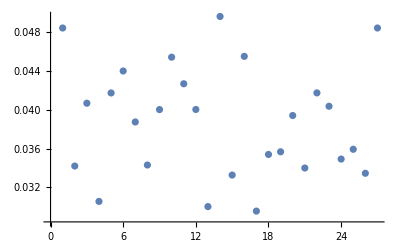

```mathematica
ListPlot@Table[MutualCoincidenceIndex[TextDecryption[ShiftDecode,k,monoblocks[[2]]],pita],{k,0,26}]
```

```mathematica
MutualCoincidenceIndex[]
```

```mathematica
MutualIncidenceIndex[textcode_,distribution_]:=
Plus@@Table[N@Count[textcode,i]distribution[[i+1]]/Length[textcode],{i,0,25}]
```

```mathematica
X4=Table[RandomInteger[25],{4000}];
```

4000

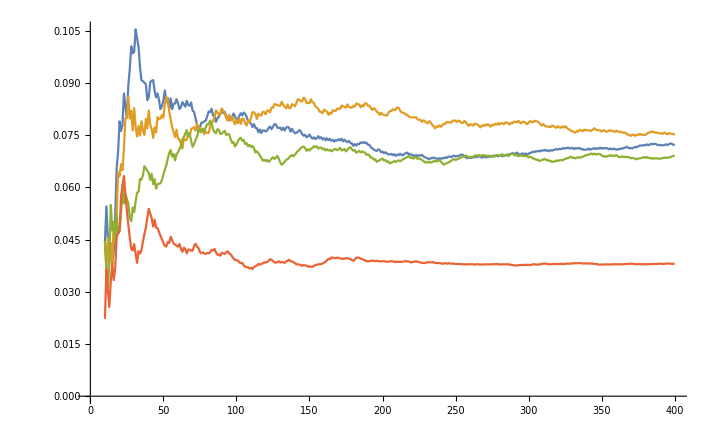

```mathematica
maxlen=Min@@Map[Length,{XN,XN2,XN3,X4}]
table=Table[{
{i,CoincidenceIndex[Take[XN,i]]},
{i,CoincidenceIndex[Take[XN2,i]]},
{i,CoincidenceIndex[Take[XN3,i]]},
{i,CoincidenceIndex[Take[X4,i]]}},{i,10,400}];
ListLinePlot[Transpose[table][[{1,2,3,4}]]]
```

```mathematica
m=26
ShiftEncode[x_,k_]:=Mod[x+k,m]
ShiftDecode[x_,k_]:=Mod[x-k,m]
```

26

```mathematica
TextEncryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,key];
	Map[encoding,text]
)]

TextDecryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,-key];
	Map[encoding,text]
)]
```

```mathematica
key=15
YN=TextEncryption[ShiftEncode,key,XN];
```

```mathematica
YN=monoblocks[[2]]
```

{21,20,21,21,20,11,13,13,25,25,20,24,25,25,21,7,11,1,21,20,11,24,20,25,0,9,0,11,1,21,9,22,19,7,18,15,7,11,9,20,15,21,20,21,9,15,11,1,22,18,24,0,9,15,25,7,11,24,18,10,15,15,15,22,24,1,0,19,25,11}

```mathematica
Manipulate[

{
Histogram[{TextEncryption[ShiftEncode,guesskey,XN2],YN},26,"Probability",ImageSize->Large],
MutualIncidenceIndex[TextDecryption[ShiftEncode,guesskey,YN],pita]
},

{guesskey,0,25,1}]
```

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[XN2,0].

Mod::argt: Mod called with 0 arguments; 2 or 3 arguments are expected.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{22,8,16,21,21,6,15,21,20,8,«8504»},0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{3,4,18,10,19,14,15,18,4,25,«35079»},0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{0.00670139,0.0116632,0.0122472,0.0122472,0.0124479,0.0160479,0.0174542,0.0174542,0.0191215,0.0241243,«110»},0].

```mathematica
Map[Hash,{483958,
525423,
504959
}]
```

{1374715000583440772,269547413338346633,8246180658051708764}

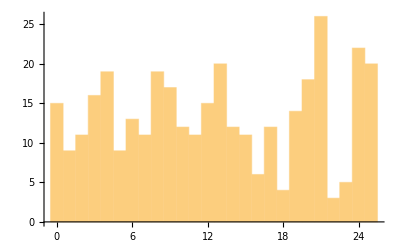

0.0424069

```mathematica
Histogram[XN=TextCode["FIOPPQNTPN BUUGGMOCYY JFMDVUUDEY ICLDYVITVL IJMMAAPYGF
            051 MOEHFKFMTV ZEIFMETVBV KDDNPFVKOI YHJZIVNRUI DCZMBKYAZX
            101 AMPEIZYEVW QOKDAPJUOK VTRKQGCZDH LFVIOIAVDM ZXHVLTJEJP
            151 EVSZUDMRUJ JUDRRCYNZJ NRJENKDTHG YJEVLRHHOK PTGLBZTJNS
            201 LINZJNVYUG ZBIBZUNFIO RNKVCHEAAU GZWEELTVMV NGPQGCVLRN
            251 WZCZCBUVZJ NIBUYMVGIT PENVYIILHN VYAYSQXROT BSYXRCAAUE
            301 YZMIGAEYZJ RTHDDQUAEZ YNVXOAKEDG MOCYYNKVTH AYDELUNUJJ
"],26]
CoincidenceIndex[XN]
```

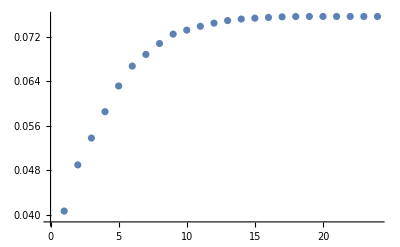

```mathematica
ListPlot[Table[Plus@@(Take[Reverse@Sort[pita],i]^2),{i,3,26}]]

Plus@@(Take[Reverse@Sort[pita],10]^2)
Plus@@(pita^2)
N[Plus@@(Table[1/26,{10}]^2)]
```

```mathematica
text=monoblocks[[2]]

LinePlot[text_]:=
(
YN=Table[

ktop=Ceiling[len/10];

focus=Take[text,len];
SB=Partition[focus,10];
stat10=Union@Flatten[Table[
					mf=Take[SortBy[Tally[SB[[k+1]]],Last],-2];
					Map[{#[[1]],Count[text,#[[1]]]}&,mf],{k,0,ktop-1}],1];
X=Map[Last,stat10];
N[Plus@@((X/Length[text])^2)],{len,10,Length[text],10}]
)
```

{8,15,12,12,24,8,12,12,12,12,3,14,21,25,23,24,3,21,25,14,23,9,3,3,9,3,21,15,9,9,1,8,7,22,21,21,25,13,6,24,24,14,2,12,9,20,23,12,21,11}

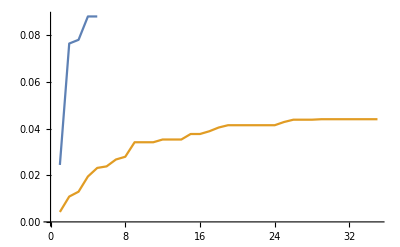
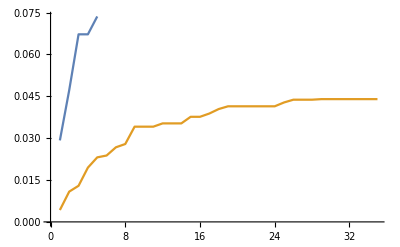
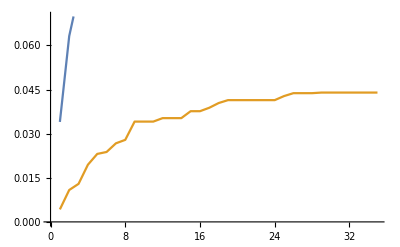
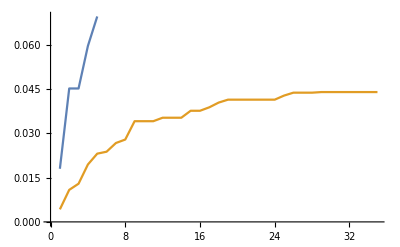
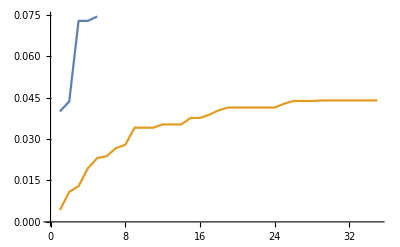
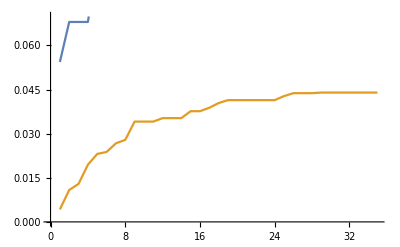
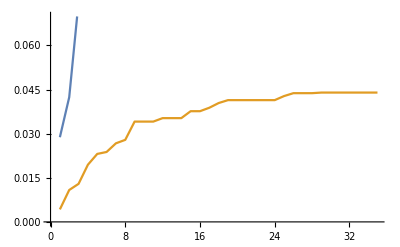

```mathematica
Map[ListLinePlot[{LinePlot[#],LinePlot[XN]}]&,monoblocks]
```

```mathematica
Map[ListLinePlot[{LinePlot[#],LinePlot[XN]}]&,monoblocks]
```

Part::partw: Part 2 of #1 does not exist.

```mathematica
Length[XN]-80
```

270

{15,16,19,9,19,12,11,15,20,11,18,26,22,20}

0.0341143

```mathematica
blocks=Partition[XN,3,1];
repetitions=Select[SortBy[Tally[blocks],#[[2]]&],#[[2]]>1&];
distanze=Flatten[Map[(indici=Flatten[Position[blocks,#[[1]]]];
distanza=(Drop[indici,1]-Drop[indici,-1]))&,repetitions]]
nguess=GCD@@distanze

monoblocks=Transpose@Partition[XN,7]

m=26
ShiftEncode[x_,k_]:=Mod[x+k,m]

TextEncryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,key];
	Map[encoding,text]
)]

TextDecryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,-key];
	Map[encoding,text]
)]

MutualCoincidenceIndex[textcode_,distribution_]:=Plus@@Table[N@Count[textcode,i] distribution[[i+1]]/Length[textcode],{i,0,25}];
```

{200,135,185,15,255,20,205,155,135,255,20,15,15,140,15}

5

{{6,20,1,20,9,6,19,4,24,9,12,1,17,21,12,2,3,17,9,21,25,21,5,19,25,1,0,7,20,6,11,19,8,11,13,2,23,6,15,25,15,3,21,15,21,2,4,15,19,3},{21,25,13,8,0,13,8,24,19,0,21,25,4,2,17,24,8,17,3,3,1,6,24,4,0,15,25,16,19,5,20,8,4,4,6,18,21,24,9,13,11,11,9,7,15,22,3,6,19,5},{2,4,21,9,12,3,12,20,7,2,2,0,1,16,1,3,15,0,8,18,3,21,22,3,2,6,17,9,7,18,19,4,15,25,24,15,13,9,13,1,17,7,10,21,18,19,7,0,12,16},{3,10,2,15,13,12,24,14,21,25,8,17,23,21,11,23,6,19,6,11,8,24,19,17,18,23,11,23,21,21,7,6,15,4,22,13,17,3,15,7,9,2,9,8,15,12,1,8,21,11},{15,21,3,5,2,17,25,21,16,23,21,11,14,2,6,20,25,13,18,0,13,9,16,4,0,13,11,14,0,21,21,9,23,14,15,6,0,7,6,6,0,18,23,12,20,16,1,21,18,15},{12,4,25,11,3,2,4,16,25,21,11,19,17,20,25,2,23,5,0,6,19,22,13,7,9,25,0,13,15,12,0,3,15,1,12,12,19,17,25,7,17,6,13,15,25,2,2,15,25,0},{20,12,2,17,4,25,25,6,23,0,7,13,0,17,2,20,7,2,8,13,21,25,6,6,4,7,13,15,15,13,21,3,5,19,6,24,13,15,7,13,24,25,1,15,15,24,21,12,17,13}}

26

{9,5,0,13,19,10,5}

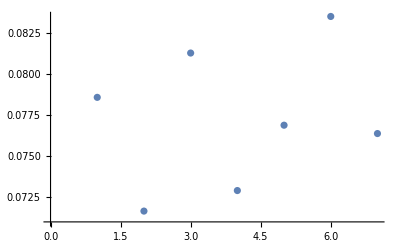

JFANTKF

{ONOCIAS,CUNONEL,PROPRIO,ORDINEI,NDIPEND,ENTIESO,VRANIIL,ORORAPP,ORTISON,OREGOLA,TIDAIPA,TTILATE,RANENSI,LEMODIF,ICAZION,IDEIPAT,TIACCET,TATEDAL,LEDUEPA,RTINONR,ICHIEDO,NOPROCE,DIMENTO,DIREVIS,IONECOS,TITUZIO,NALEART,TUTTELE,CONFESS,IONIREL,IGIOSES,ONOEGUA,LMENTEL,IBEREDA,VANTIAL,LALEGGE,LECONFE,SSIONIR,ELIGIOS,EDIVERS,EDALLAC,ATTOLIC,AHANNOD,IRITTOD,IORGANI,ZZARSIS,ECONDOI,PROPRIS,TATUTII,NQUANTO}

{69,315,7,217,315,217,315,114,35,315,119,21,189,63,67,7,35,55}

1

{{5,19,6,5,4,21,12,5,5,5,10,10,8,2,25,25,10,10,2,8,25,4,20,20,25,10,4,10,19,25,25,5,2,25,12,2,2,9,21,21,21,17,17,25,25,16,21,6,10,4},{8,15,12,12,24,8,12,12,12,12,3,14,21,25,23,24,3,21,25,14,23,9,3,3,9,3,21,15,9,9,1,8,7,22,21,21,25,13,6,24,24,14,2,12,9,20,23,12,21,11},{14,13,14,3,8,19,0,14,19,4,3,8,13,12,0,4,0,19,3,8,7,15,12,17,13,19,11,19,13,13,8,14,4,4,13,11,2,8,8,8,0,19,0,8,17,0,14,14,19,20},{15,1,2,21,2,21,0,4,21,19,13,24,17,1,12,21,15,17,7,0,21,4,17,17,17,7,17,6,18,21,1,17,0,4,6,17,1,1,19,8,24,1,0,6,19,4,0,2,7,13},{15,20,24,20,11,11,15,7,25,21,15,7,20,10,15,22,9,10,11,21,11,21,20,2,9,6,7,11,11,24,25,13,0,11,15,13,20,20,15,11,18,18,20,0,7,25,10,24,0,20},{16,20,24,20,3,8,24,5,4,1,5,9,8,24,4,16,20,16,5,3,19,18,9,24,4,24,7,1,8,20,20,10,20,19,16,22,21,24,4,7,16,24,4,4,3,24,4,24,24,9},{13,6,9,3,24,9,6,10,8,21,21,25,3,0,8,14,14,6,21,12,9,25,9,13,13,9,14,25,13,6,13,21,6,21,6,25,25,12,13,13,23,23,24,24,3,13,3,13,3,9}}

26

{9,5,0,13,19,10,5}

JFANTKF

```mathematica
key=Map[(mindexes=Table[
MutualCoincidenceIndex[TextDecryption[ShiftDecode,keyguess,#],pita],{keyguess,0,26}];
Position[mindexes,Max[mindexes]][[1,1]]-1)&,monoblocks]


allbestindexes=Map[(mindexes=Table[
MutualCoincidenceIndex[TextDecryption[ShiftDecode,keyguess,#],pita],{keyguess,0,26}];
Max[mindexes])&,monoblocks];
ListPlot[allbestindexes]


FromCode[key]

FromCode[Transpose@MapThread[TextDecryption[ShiftDecode,#1,#2]&,{key,monoblocks}]]
```

```mathematica
TextCode["GVCDPMUUZE KVEMBNVCDZ CUIJPFLRJA MNCDEGNDMR CZTIMYZEZE
            051 YUOVQGYTHV QZXJACZXVA MVCIVLHBZA RLTNREBXOR AVCQVCURMR
            101 BLGZCCYDXU CUDIPGZXHR RATNFCJDIG SAIVDSLAGN ZBDINTVVGV
            151 YJWZFYWTQN GTEDREHGZA CSAJEBPGXN ZHAZRLLANH QJXONPUTHV
            201 APPGFSVVMN LUTHVAVTIE GJDDIEPPXP FLEZEOBTNG YWPMGCSPNG
            251 MYXVNRATNG YJDHRPPJNP GZHZNBHGHN PLRJARYDLH CSGZVJKJXN
            261 BPHVIMPPVP SPUZPCWTMQ CYEDHBBCVP GAIVPMTTMV SZRDFQLPAN
"]
```

GVCDPMUUZE KVEMBNVCDZ CUIJPFLRJA MNCDEGNDMR CZTIMYZEZE
            051 YUOVQGYTHV QZXJACZXVA MVCIVLHBZA RLTNREBXOR AVCQVCURMR
            101 BLGZCCYDXU CUDIPGZXHR RATNFCJDIG SAIVDSLAGN ZBDINTVVGV
            151 YJWZFYWTQN GTEDREHGZA CSAJEBPGXN ZHAZRLLANH QJXONPUTHV
            201 APPGFSVVMN LUTHVAVTIE GJDDIEPPXP FLEZEOBTNG YWPMGCSPNG
            251 MYXVNRATNG YJDHRPPJNP GZHZNBHGHN PLRJARYDLH CSGZVJKJXN
            261 BPHVIMPPVP SPUZPCWTMQ CYEDHBBCVP GAIVPMTTMV SZRDFQLPAN